```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g- t- t (1-loop)

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 2 Particles insertions

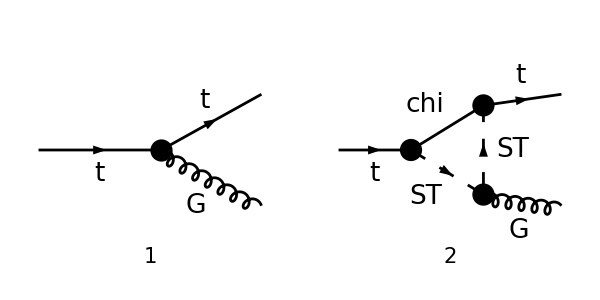

```mathematica
tops0 = CreateTopologies[0,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  {F[9]}->  {F[9], V[4]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p1},OutgoingMomenta->{-p2,-p3},LoopMomenta->{q},List->False,SUNIndexNames->{aa,bb,cc3},SUNFIndexNames->{c1,c2,a},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampA,{p3->-p1-p2}]]]]
```

in total: 2 Particles amplitudes

gs T_c2c1^cc3 ((yDM^2 (γ·q).(γ̄)^6 (-p1^μ+p2^μ+2 q^μ))/((q^2-mChi^2).((p2+q)^2-mST^2).((q-p1)^2-mST^2))+ⅈ (2 π^2 deltaCTL yDM^2+1) γ^μ.(γ̄)^7+ⅈ (2 π^2 deltaCTR yDM^2+1) γ^μ.(γ̄)^6)

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify),LorentzIndexNames-> {μ,ν}]
```

ⅈ gs T_c2c1^cc3 (2 π^2 yDM^2 γ^μ.(γ̄)^6 C_00(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+π^2 yDM^2 (p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 π^2 yDM^2 p1^μ (γ·p1).(γ̄)^6 C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-2 π^2 yDM^2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-π^2 yDM^2 (p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_2(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 π^2 yDM^2 p2^μ (γ·p2).(γ̄)^6 C_22(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+γ^μ.((γ̄)^6+(γ̄)^7)+2 π^2 deltaCTL yDM^2 γ^μ.(γ̄)^7+2 π^2 deltaCTR yDM^2 γ^μ.(γ̄)^6)

```mathematica
(* Remove SM contribution *)
ampSM=gs SeriesCoefficient[ampC,{gs,0,1},{yDM,0,0}];
ampC=Simplify[DiracSimplify[ampC-ampSM]];
```

## Off - Shell Case

```mathematica
FCClearScalarProducts[];
```

```mathematica
SPD[p1,p2]=1/2(s-SPD[p1,p1]-SPD[p2,p2]);
```

```mathematica
ampD=FullSimplify[DiracSimplify[FCReplaceMomenta[ampC,{p3->-p1-p2}]]];
```

```mathematica
ampEsimp2=FullSimplify[ExpandScalarProduct[DiracSimplify[ampD/.{DiracGamma[7]->1-DiracGamma[6]}]]];
```

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]]]},{i,1,Length[lInts]}]
```

(C_1(p1^2,s,p2^2,mChi^2,mST^2,mST^2) | 0
C_2(p1^2,s,p2^2,mChi^2,mST^2,mST^2) | 0
C_00(p1^2,s,p2^2,mChi^2,mST^2,mST^2) | 1/(4 ε_UV)
C_11(p1^2,s,p2^2,mChi^2,mST^2,mST^2) | 0
C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2) | 0
C_22(p1^2,s,p2^2,mChi^2,mST^2,mST^2) | 0)

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp2,PaXImplicitPrefactor->1/(2 Pi)^(4)]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[SUNSimplify[Coefficient[ampEsimp2,deltaCTR]] (-1/(64 Pi^4  EpsilonUV))];
FullSimplify[FeynAmpDenominatorExplicit[DiracSimplify[loopUV+ctUV,DiracSubstitute67->False]]]
```

0

## Coefficients for Loop Amplitude

```mathematica
args1={Pair[Momentum[p1,D],Momentum[p1,D]],s,Pair[Momentum[p2,D],Momentum[p2,D]]};
args2={mChi^2,mST^2,mST^2};
argsNew={p1sq,s,p2sq};
subs2={PaVe[0,0,args1,args2,a___]->C00eff@@argsNew+deltaCTL-deltaCTR,PaVe[1,1,args1,args2,a___]->C11@@argsNew,PaVe[2,2,args1,args2,a___]->C22@@argsNew,PaVe[1,2,args1,args2,a___]->C12@@argsNew,PaVe[1,args1,args2,a___]->C1@@argsNew,PaVe[2,args1,args2,a___]->C2@@argsNew};
```

```mathematica
ampEsimp3=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp2]]/.subs2;
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]];
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains4=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[Join[spinorChains1,spinorChains2,spinorChains3,spinorChains4]]
pairs1=Cases2[ampEsimp3,Pair];
pairs2=Flatten[Table[pairs1[[i]] pairs1[[j]],{i,1,Length[pairs1]},{j,i+1,Length[pairs1]}]];
allPairs=Join[pairs1,pairs2]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
```

{(γ̄)^6,γ^μ,γ·p1,γ·p2,γ^μ.(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6}

{p1^μ,p2^μ,p1^μ p2^μ}

{T_c2c1^cc3}

### Coefficients for each term

Define shortnames for each coefficient

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]],allPairs[[k]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs yDM^2),{MT,t,u},FullSimplify];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],allPairs[[k]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]},{k,1,Length[allPairs]}];
```

We have to deal with the terms without explicit momenta separately:

```mathematica
Do[c=FullSimplify[Coefficient[Coefficient[Expand[ampEsimp3/.{Pair[LorentzIndex[μ,D],Momentum[p2,D]]->0,Pair[LorentzIndex[μ,D],Momentum[p1,D]]->0}],su3prods[[i]]],allTerms[[j]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs yDM^2),{MT,t,u},FullSimplify];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],1,c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs yDM^2  Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]]su3Terms[[i,4]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEsimp3]
```

0

```mathematica
su3Terms
```

(T_c2c1^cc3 | (γ·p1).(γ̄)^6 | p1^μ | C1(p1sq,s,p2sq)+2 C11(p1sq,s,p2sq)
T_c2c1^cc3 | (γ·p1).(γ̄)^6 | p2^μ | -C1(p1sq,s,p2sq)-2 C12(p1sq,s,p2sq)
T_c2c1^cc3 | (γ·p2).(γ̄)^6 | p1^μ | -2 C12(p1sq,s,p2sq)-C2(p1sq,s,p2sq)
T_c2c1^cc3 | (γ·p2).(γ̄)^6 | p2^μ | C2(p1sq,s,p2sq)+2 C22(p1sq,s,p2sq)
T_c2c1^cc3 | γ^μ | 1 | 2 deltaCTL
T_c2c1^cc3 | γ^μ.(γ̄)^6 | 1 | 2 C00eff(p1sq,s,p2sq))

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3) ] (all momenta are incoming)
c2 = Top color = "2", c1 = Anti-Top color = "1", c3 = Gluon color = "3"
spins = [2, 2, 3], 
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contract to the left and the first (incoming) to the right)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
momenta=Tally[su3Terms[[All,3]]][[All,1]]
```

{T_c2c1^cc3}

{(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,γ^μ,γ^μ.(γ̄)^6}

{p1^μ,p2^μ,1}

```mathematica
su3Replacements={SUNTF[{SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]-> "T(3,2,1)"};
tensorReplacements={DiracGamma[Momentum[p1,D],D].DiracGamma[6]-> "P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1)",
				   DiracGamma[Momentum[p2,D],D].DiracGamma[6]-> "P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1)",
				   DiracGamma[LorentzIndex[μ,D],D]-> "Gamma(3,2,1)",
				    DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6]-> "Gamma(3,2,-1)*ProjP(-1,1)"};
momentaReplacements={ Pair[LorentzIndex[μ,D],Momentum[p1,D]]-> "P(3,1)*",
                                           Pair[LorentzIndex[μ,D],Momentum[p2,D]]-> "P(3,2)*",1-> ""};
```

```mathematica
tensorReplacements = SortBy[tensorReplacements,-StringLength[ToString[#]]&]
momentaReplacements
```

{(γ·p1).(γ̄)^6→P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1),(γ·p2).(γ̄)^6→P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1),γ^μ.(γ̄)^6→Gamma(3,2,-1)*ProjP(-1,1),γ^μ→Gamma(3,2,1)}

{p1^μ→P(3,1)*,p2^μ→P(3,2)*,1→}

```mathematica
vertexCounter=0;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Print[StringJoin["FFVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n   + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr," )"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

------------------

T(3,2,1)

FFVNP1

( P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1) )*( P(3,1)*(C1(p1sq,s,p2sq) + 2*C11(p1sq,s,p2sq))\
   + P(3,2)*(-C1(p1sq,s,p2sq) - 2*C12(p1sq,s,p2sq)) )

FFVNP2

( P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1) )*( P(3,1)*(-2*C12(p1sq,s,p2sq) - C2(p1sq,s,p2sq))\
   + P(3,2)*(C2(p1sq,s,p2sq) + 2*C22(p1sq,s,p2sq)) )

FFVNP3

( Gamma(3,2,1) )*( (2*deltaCTL) )

FFVNP4

( Gamma(3,2,-1)*ProjP(-1,1) )*( (2*C00eff(p1sq,s,p2sq)) )

#### Write to File

```mathematica
fileName="../../Models/Top-FormFactorsOneLoop-UFO/lffvnp.txt";
outF = OpenWrite[fileName,PageWidth->Infinity];
vertexCounter=0;
Do[
Write[outF,"------------------"];
Write[outF,su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Write[outF,StringJoin["FFVNP",ToString[vertexCounter]]];
(* Write[outF,tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n   + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr," )"];
 Write[outF,fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
Close[outF]
```

../../Models/Top-FormFactorsOneLoop-UFO/lffvnp.txt